## Undamped noisy oscillator (Problem 8.7)

Define the (discretized) system, with noisy inputs

```mathematica
Clear["Global`*"];
SetOptions[ListPlot,Joined->True,InterpolationOrder->0,PlotRange -> All];
Ts=0.1;  Tend = 15; Nt =Round[Tend/Ts];  (* # time steps to simulate *)

G1ss=StateSpaceModel[{x''[t]+x[t]==u[t]+w[t]},{{x[t],0},{x'[t],0}},{{u[t],0},{w[t],0}},{x[t]},t] (* undamped oscillator; separate inputs for fb, noise *);
G1dss = ToDiscreteTimeModel[G1ss,Ts,z,Method -> "ZeroOrderHold"];
zeroIn= Table[0,{i,Nt}] (* zero input *);
ν=0.3; ξ=0.3         (* proc. & meas. noise *);
SeedRandom[2]     (* for reproducible plots *) 
processNoise=RandomReal[NormalDistribution[0,ν],Nt];
measurementNoise=RandomReal[NormalDistribution[0,ξ],Nt];
```

RandomGeneratorState[…]

Open loop disturbance response, using Kalman filter (current observer)

```mathematica
kalEst=KalmanEstimator[{G1dss,All,1},{({{ν^2}}),({{ξ^2}})}];
ym=Flatten[OutputResponse[{G1dss,{0,1}},{zeroIn,processNoise}]]+measurementNoise         (* noisy position measurement *);
{xs,vs}=StateResponse[{G1dss,{0,1}},{zeroIn,processNoise}] (* physical states *);
{xe,ve,ye}=OutputResponse[kalEst,{zeroIn,ym}];  (* Kalman estimate *)

dr=DataRange->{0,Tend}; lRed=Lighter[Red,0.7];plotmax=1.5;plot0a=ListPlot[{ym,xe,xs},dr,PlotStyle ->{lRed,Black,Blue},PlotRange->{-plotmax,plotmax}];
```

LQG controller for disturbance response  (explicit construction)

```mathematica
q=({{1, 0}, {0, 1}}); r={{0.1}} (* weight matrices for state, input *);k=LQRegulatorGains[{G1dss,1},{q,r}]
```

{{1.74136,3.26058}}

```mathematica
l=LQEstimatorGains[{G1dss,All,1},{({{ν^2}}),({{ξ^2}})}]
```

{{0.0869569},{0.0395135}}

```mathematica
{a,b,c,d}=Normal[SystemsModelExtract[G1dss,1]];
{Eigenvalues[a],Eigenvalues[a-KroneckerProduct[b,k]]}
```

{{0.995004+0.0998334 ⅈ,0.995004-0.0998334 ⅈ},{0.875106,0.780688}}

```mathematica
(* the closed-loop sys is overdamped, but not by much *)
```

```mathematica
a1= ArrayFlatten[({{a, -b.k}, {l.c.a, a-b.k-l.c.a}})]  ;b1=ArrayFlatten[({{b, 0}, {l.c.b, l}})]  (* inputs = (ν,ξ) *);c1=({{1, 0, 0, 0}});
closedLoop2=StateSpaceModel[{a1,b1,c1},SamplingPeriod->Ts];

{xs2,vs2,xe2,ve2}=StateResponse[{closedLoop2,{0,1,0,0}},{processNoise,measurementNoise}];
ym2=xs2+measurementNoise;
pclosed2=ListPlot[{ym2,xe2,xs2},dr,PlotStyle ->{lRed,Black,Blue},PlotRange->{-plotmax,plotmax}];
pclosed3=ListPlot[{xs-xe,xs2-xe2,xs-xe-xs2+xe2 },dr,PlotRange->{-0.3,0.5}];
```

Graphs

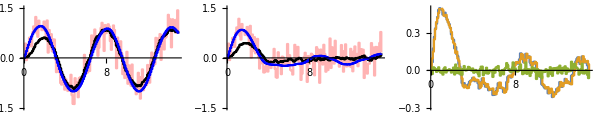

```mathematica
GraphicsRow[{plot0a,pclosed2,pclosed3},ImageSize->600]
```

```mathematica
StandardDeviation/@{Take[xs2,-50],Take[xe2,-50]}  (* sd of last 50 elements *)
```

{0.102521,0.0405857}

Show the systems explicitly

```mathematica
{G1ss,G1dss,closedLoop2}
```

{0100-10111000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2121FalseFalseFalseAutomaticNone,{{x[t],0},x_1},{{u[t],0},{w[t],0}},Automatic,t,0.9950040.09983340.004995830.00499583-0.09983340.9950040.09983340.099833410000.1StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2121FalseFalseFalseAutomaticNone,Automatic,{{u[z],0},{w[z],0}},Automatic,z,0.9950040.0998334-0.00869953-0.01628930.004995830-0.09983340.995004-0.173846-0.3255150.099833400.08652250.008681210.8997820.07486290.0004344220.08695690.03931610.00394477-0.3129950.6655450.0001974030.03951351000000.1StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2141FalseFalseFalseAutomaticNoneAutomatic}

Export data

```mathematica
(* 
SetDirectory[NotebookDirectory[]];
Export["UndampedNoisyOscillator.dat", {ym,xe,xs,ym2,xe2,xs2}ᵀ];
*)
```